# GPX file analysis

#### Basic Mapping Analysis

```mathematica
gpx=Import["C:\\Users\\arnoudb.WRI\\Downloads\\kuhkopfsteig-fv\\kuhkopfsteig-fv.gpx","XML"];
```

```mathematica
data=Cases[gpx,
XMLElement[
"trkpt",
{"lat"->lat_,"lon"->lon_},{
XMLElement["ele",{},{ele_}],
XMLElement["time",{},{time_}]
}]:>{
DateObject[time],
GeoPosition[ToExpression/@{lat,lon,ele}]
},∞];
```

```mathematica
data=Map[{
TimeObject[ToExpression/@StringSplit[StringSplit[First[#],"T"|" Z)"][[-1]],":"]],#}&,
rawData];
```

```mathematica
Take[data,10]//Grid
```

Mon 3 Dec 2012 09:08:42GMT-5. | GeoPosition[{50.7168,6.44562,166.45}]
Mon 3 Dec 2012 09:08:43GMT-5. | GeoPosition[{50.7168,6.44562,166.45}]
Mon 3 Dec 2012 09:08:44GMT-5. | GeoPosition[{50.7168,6.44562,166.45}]
Mon 3 Dec 2012 09:08:58GMT-5. | GeoPosition[{50.7168,6.44562,166.45}]
Mon 3 Dec 2012 09:09:08GMT-5. | GeoPosition[{50.7168,6.44565,166.45}]
Mon 3 Dec 2012 09:09:18GMT-5. | GeoPosition[{50.7168,6.44566,166.93}]
Mon 3 Dec 2012 09:09:24GMT-5. | GeoPosition[{50.7168,6.44562,166.93}]
Mon 3 Dec 2012 09:09:29GMT-5. | GeoPosition[{50.7167,6.4456,167.41}]
Mon 3 Dec 2012 09:09:38GMT-5. | GeoPosition[{50.7167,6.44561,167.41}]
Mon 3 Dec 2012 09:09:39GMT-5. | GeoPosition[{50.7167,6.44561,167.41}]

```mathematica
GeoGraphics[{AbsoluteThickness[2],Orange,JoinForm["Bevel"],Line[data[[All,2]]]},GeoRange->Quantity[3,"Kilometers"]]
```

-Graphics-

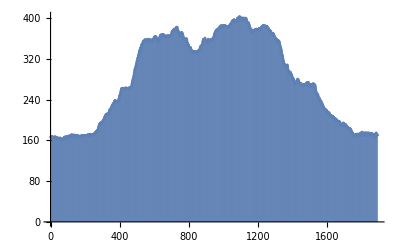

```mathematica
elevationPlot=ListPlot[data[[All,2,1,3]],Filling->Axis]
```

#### Speed Analysis

```mathematica
{pt1,pt2}=data[[1000;;1001]][[All,2]]
```

{GeoPosition[{50.7062,6.46137,383.7}],GeoPosition[{50.7063,6.46118,384.66}]}

```mathematica
distance=UnitConvert[GeoDistance[pt1,pt2],"Kilometers"]
```

0.0182683 km

```mathematica
{t1,t2}=data[[1000;;1001]][[All,1]]
```

{Mon 3 Dec 2012 11:24:35GMT-5.,Mon 3 Dec 2012 11:24:49GMT-5.}

```mathematica
timedelta=DateDifference[t1,t2,"Hour"]
```

0.00388889 h

```mathematica
distance/timedelta
```

4.69757 km/h

```mathematica
Length[data]
```

1890

```mathematica
speeds=Table[
Module[{p1,p2,distance,t1,t2,delta},
{{t1,p1},{t2,p2}}=data[[i;;i+1]];
distance=UnitConvert[GeoDistance[p1,p2],"Kilometers"];
delta=DateDifference[t1,t2,"Hour"];
distance/delta
],{i,Length[data]-1}];
```

```mathematica
ListLinePlot[speeds]
```

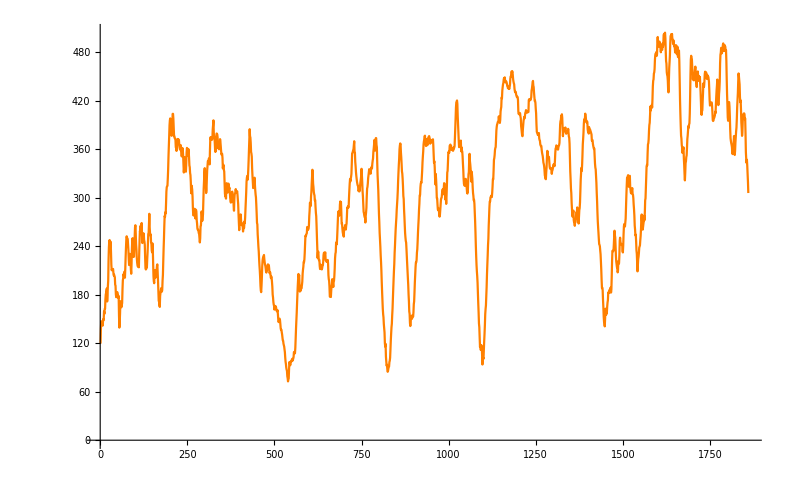

```mathematica
speedPlot=ListLinePlot[100MovingAverage[speeds,30],PlotStyle->Orange]
```

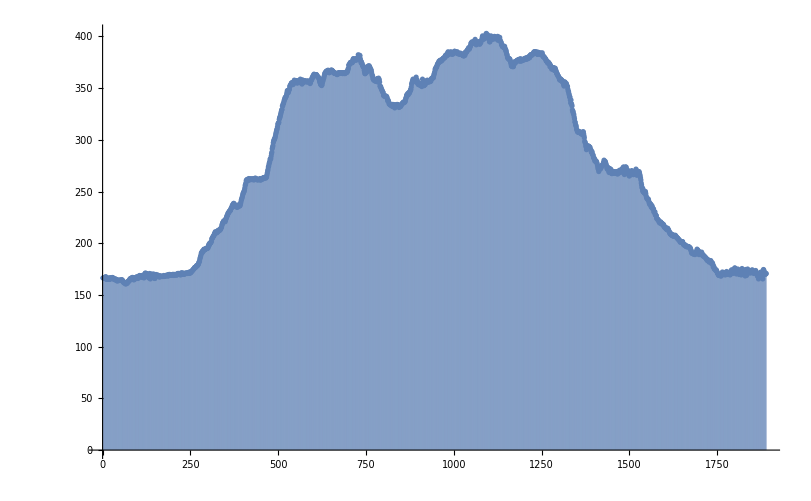

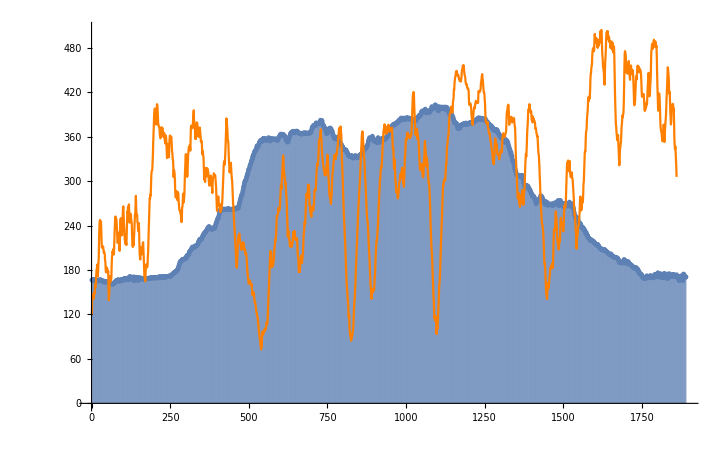

```mathematica
Show[{elevationPlot,speedPlot},PlotRange->All]
```

#### Waypoints Analysis

```mathematica
wayPoints=Cases[gpx,XMLElement[
"wpt",
{"lat"->lat_,"lon"->lon_},{
XMLElement["ele",{},{ele_}],
XMLElement["time",{},{time_}],
XMLElement["name",{},{name_}],
XMLElement["sym",{},sym_],
XMLElement["type",{},{type_}],
_}]:>{lat,lon,ele,time,name,sym}
,
∞];
```

```mathematica
flag[pos_,{color_}]:=GeoMarker[pos,Graphics[{ToExpression[StringSplit[color,", "][[-1]]],Rectangle[{0,0},{1,1}]}],"Scale"->Scaled[0.01]]
```

```mathematica
flag[pos_,{"Flag, Blue"}]:=GeoMarker[pos,Graphics[{Black,AbsoluteThickness[2],Circle[],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}],Darker[Blue],Disk[{0,0},0.6]}],"Scale"->Scaled[0.02]]
```

```mathematica
flag[pos_,{"Civil"}]:=GeoMarker[pos,Graphics[{Orange,Rectangle[{0,0},{1,1}]}],"Scale"->Scaled[0.01]]
```

```mathematica
flag[pos_,{"Crossing"}]:=GeoMarker[pos,Graphics[{Purple,Rectangle[{0,0},{1,1}]}],"Scale"->Scaled[0.01]]
```

```mathematica
wayPointMarkers=Map[flag[GeoPosition[ToExpression/@{First[#],#[[2]]}],Last[#]]&,wayPoints[[All,{1,2,-1}]]];
```

```mathematica
GeoGraphics[Join[{AbsoluteThickness[2],Orange,JoinForm["Bevel"],Line[data[[All,2]]]},wayPointMarkers],GeoRange->Quantity[3,"Kilometers"]]
```

-Graphics-